```mathematica
(*DEFINITION OF FUNCTIONS *)
ClearAll[angle,t,g,b1,b2,b3]

(*This function draws an inclined plane of variable inclination with a ball*)
inclinedPlane[angle_, t_, g_, b1_, b2_, b3_]:= 

DynamicModule[
	{θ, lengthPlane,heightPlane, h, dFall, yFall, xFall, timeFall, ϕ, ballRadius, ballCenter, ballPoint, lineBells, bellOne, t3, bellTwo, t2, bellThree, t1, bellEnd, tf},
	θ = angle * π/180;(*inclination angle of the plane in radians*)
	lengthPlane = 400;
	heightPlane = lengthPlane * Sin[θ]; (*height of the plane*)
	h = lengthPlane * Sin[θ]+2*ballRadius*Cos[θ]; (*height of the line of bells*)
    dFall = 1/2*g*Sin[θ]*t^2;(*distance falling on the plane*)
	yFall = -dFall*Sin[θ];(*vertical distance of falling*)
	xFall = dFall*Cos[θ];(*horitzontal distance of falling*)
	ballRadius=10;
	ϕ = dFall/ballRadius;(*angle rotating by the ball rolling down the plane*)
	ballCenter ={ballRadius*Sin[θ]+xFall, heightPlane+ballRadius*Cos[θ]+yFall};
	ballPoint = ballCenter + {ballRadius*Sin[θ],ballRadius*Cos[θ]};
	lineBells = {{2*ballRadius*Sin[θ],lengthPlane*Sin[θ]+2*ballRadius*Cos[θ]},{lengthPlane*Cos[θ]+2*ballRadius*Sin[θ],2*ballRadius*Cos[θ]}};
	bellEnd = pointLine[1,lineBells]; (*point location of the last fixed bell*)
	bellOne = pointLine[b1,lineBells]; (*point location of the first mobile bell*)
	bellTwo = pointLine[b2,lineBells]; (*point location of the second mobile bell*)
	bellThree = pointLine[b3,lineBells]; (*point location of the third mobile bell*)
	t1 = Round[√(2*(h - bellThree[[2]])/(g*(Sin[θ])^2)),0.1];(*time of first collision ball-bell*)
	t2 = Round[√(2*(h - bellTwo[[2]])/(g*(Sin[θ])^2)),0.1];(*final of the second collision ball-bell*)
	t3 = Round[√(2*(h - bellOne[[2]])/(g*(Sin[θ])^2)),0.1];(*time of the third collision ball-bell*)
	tf = Round[√(2*(lengthPlane-ballRadius)/(g*Sin[θ])),0.1];(*final time of falling on an inclined Plane*)
	bells = {0,b3,b2,b1,1};(*is a global list variable that store the position of the balls as a ratio of lengthplane*)
	timeBells = {0,t1,t2,t3,tf};(*is a global list variable that store all the times of collisions ball-bell*)
	DynamicWrapper[	
    Graphics[
		{
		(*draws the plane*)
		Style[Line[{{0,lengthPlane*Sin[θ]},{lengthPlane*Cos[θ],0}}],Blue,Thick],

		(*draws the ball*)
		Style[Circle[ballCenter,ballRadius],Red,Thick] ,
		
		(*draws ballPoint*)
		{PointSize[Large],Red,Point[ballPoint]},
		
		(*draws the final stop mark on the plane *)		
		Style[Line[{{lengthPlane*Cos[θ],0},{lengthPlane*Cos[θ]+2*ballRadius*Sin[θ],2*ballRadius*Cos[θ]}}],Blue,Thick],

		(*draws the line for the bells *)
		Line[lineBells],
	
		(*draws the bells *)
		PointSize[Large],
		Point[bellEnd], (*point location of the last fixed bell*)
		Point[bellOne], (*point location of the first mobile bell*)
		Point[bellTwo], (*point location of the second mobile bell*)
		Point[bellThree], (*point location of the third mobile bell*)
		
		
		(*draws the radius of the ball*)
		Style[Line[{ballCenter,ballCenter+ballRadius*{-Sin[θ+ϕ],-Cos[θ+ϕ]}}],Red],

		(*draws the inclination arc of the plane*)	
		Style[Circle[{lengthPlane*Cos[θ],0},100,{π-θ,π}],Blue]					
		},
	(*plot the labels*)
	PlotLabel->Style[Row[
						{
						"θ = ",angle,"°",
						"  a = ",Round[g* Sin[θ],0.1]," m/",Superscript["s",2],
						"  t = ",Round[t,0.1],
						" t1 = ",t1,
						" t2 = ",t2,
						" t3 = ",t3,
						" tf = ",tf						
						}
						],
						Black,"Label",10],
	PlotRange->{{0,400},{0,300}},
	ImageSize->425,
	Frame->True
	],
	
	(*emits sound when the ball touch the bells*)
	If[
		(*EuclideanDistance[bellThree[[1]],ballPoint] < radiusFall[angle, lengthPlane, g , ballPoint[[2]], 0.04]*)
		t1 - 0.1 < Round[t,0.01]< t1 + 0.1 ,
		EmitSound[Sound[SoundNote[]]],
			If [
			(*EuclideanDistance[bellTwo[[1]],ballPoint] < radiusFall[angle, lengthPlane, g , ballPoint[[2]], 0.04]*)
			t2 - 0.1 < Round[t,0.01]< t2 + 0.1 ,
			EmitSound[Sound[SoundNote[]]],
				If[
				(*EuclideanDistance[bellOne[[1]],ballPoint] < radiusFall[angle, lengthPlane, g , ballPoint[[2]], 0.05]*)
				t3 - 0.1 < Round[t,0.01]< t3 + 0.1 ,
				EmitSound[Sound[SoundNote[]]],
					If[
						tf - 0.2 < Round[t,0.01]  ,
						EmitSound[Sound[SoundNote[]]]
					]
				]
			]
		]
	]
];

(*This function locate a bell on the line of bells*)
ClearAll[bell,lines]
pointLine[bell_,lines_]:=
Module[{pointLine,startPoint,finalPoint,direction},
	startPoint = lines[[1]];
	finalPoint = lines[[2]];
	direction = finalPoint - startPoint;
	pointLine = startPoint + bell*direction
	];


(*This function compute the final time of falling on an inclined Plane*)
ClearAll[angle,lengthPlane,g]
timeFall[angle_,lengthPlane_,g_]:=
Module[{θ,finalTime,ballRadius},
	θ = angle * π/180;
	ballRadius = 10;
	finalTime = √(2*(lengthPlane-ballRadius)/(g*Sin[θ]))
	];
	
(*This function compute the radius of proximity between the ball and the bell to emit sound*)
ClearAll[angle,lengthPlane,δ,y]
radiusFall[angle_, lengthPlane_, g_ , y_, δ_]:=
Module[{θ,ballRadius,v,h,R},
	θ = angle * π/180;
    ballRadius=10;
	h = lengthPlane * Sin[θ]+2*ballRadius*Cos[θ]; (*height of the line of bells*)
	v = √(2*g*(h-y)); (*speed of falling on the plane*)
	R = Round[v * δ,0.01](*radius of detection between the ball and the bells for emit sound*)
	];


(*This function map a list of Solar planets taking its gravity and and its images*)
ClearAll[planets]
menuPlanet[planets_]:=
Module[{menuSolar},
		menuSolar = Map[QuantityMagnitude[UnitConvert[#["Gravity"],"SI"]]-> Row[{#,#["Image"]}]&,planets]
	]
```

```mathematica
Manipulate[

inclinedPlane[angle, t, g, b1, b2,b3],

(*configuration of controls*)
	(*the angle is measured in degrees*)
	{{angle,5,"slope θ"},5,45,5,ControlType->Slider} ,
	
	(*the position of the intermediate bells between the start and the end of the plane*)
	{{b1,0,"bell 1"},0,1,0.01,ControlType->Automatic},
	{{b2,0,"bell 2"},0,b1,0.01,ControlType->Automatic},
	{{b3,0,"bell 3"},0,b2,0.01,ControlType->Automatic},
	
		
	(*the time is in seconds*)
	{{t,0.001,"release ball"},0.001,timeFall[angle,400,g],0.001,Trigger,AnimationRate->1,Appearance->"Labeled",ControlPlacement->Left},
		
	(*gravitational constant of Solar system planets*)
	{{g,9.8`3.,"Planet:"},menuPlanet[PlanetData[]]},ControlType->PopupMenu,

		
	SaveDefinitions->True,
	ControlPlacement->Left
]
```

The sound of the bells when the ball is passing at each check point can be registered with an AudioCapture[ ] command and saved with a name audio file .wav in the user’s current directory of work. The record button must be pressed after release the ball and stopped after the ball is fallen:

```mathematica
soundBells = AudioCapture["Earth_25deg_075050025.wav"]
```

```mathematica
soundBells =
```

We audio recording of the bells c or an be now analyzed with an spectrogram or an audio plot to deduce the time of each collision between the ball and the bells:

```mathematica
spectroBells=Spectrogram[soundBells]
```

-Graphics-

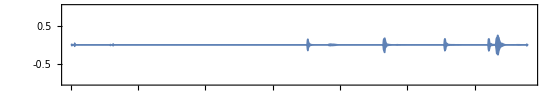

```mathematica
plotBells = AudioPlot[soundBells]
```

With the same values of inclination angle, planet and position of the bells, we can do the falling experiment more times to reduce the experimental errors of registering the collision events. And after that we include the values of collisions time a list variable timeBells = {0,t_1,t_2,t_3t_f}. The variable timeBells is defined as a global variable into the code of the functions defined, so we can also call directly the variable and it will take the internal times computed by the algorithm of simulation fall.

Now we can call the variable bells and the variable timeBells with the values of the falling:

```mathematica
bells
```

{0,0.25,0.5,0.75,1}

```mathematica
timeBells
```

{0,3.8,5.3,6.5,7.4}

The positions of the bells are given as a fraction of the length of the plane that is stored in the local variable lengthplane. In the previous case we have taken the value lengthplane = 400 (in dimensionless units of distance). So the distances traveled by the ball until touch the bells are:

```mathematica
spaceBells = 400 * bells
```

{0,100.,200.,300.,400}

With the list  spaceBells and timeBells we can make a table of points {space,time} to see how the space traveled by the ball is changing when the time is changing:

```mathematica
ballBells= Table[{timeBells[[i]],spaceBells[[i]]},{i,1,5}]
```

{{0,0},{3.8,100.},{5.3,200.},{6.5,300.},{7.4,400}}

If we visualize that list of data points in a graphic time vs space we obtain:

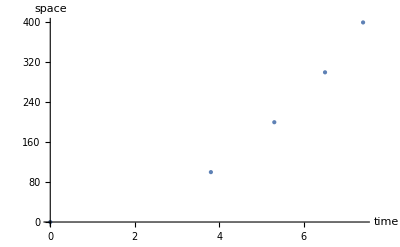

```mathematica
ListPlot[ballBells,AxesLabel->{"time","space"},PlotStyle->PointSize[Large]]
```

And joining the points with lines:

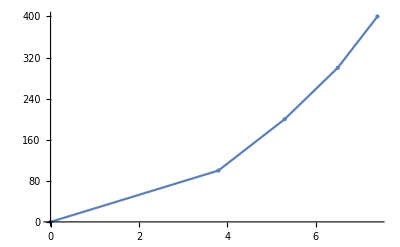

```mathematica
Show[ListLinePlot[ballBells],ListPlot[ballBells,AxesLabel->{"time","space"},PlotStyle->PointSize[Large]]]
```

We can ask to you, well, which kind of natural law is behind that pattern of points? There is any mathematical curve that fits the data? To answer that we use the function Interpolation[ ]: to define the function distance as a function of time:

```mathematica
distance = Interpolation[ballBells]
```

InterpolatingFunction[{{0., 7.4}}, <>]

Now we can call the function distance[t] to predict the value of the space traveled by the falling ball the time is t, for example for t = 1s we’ll have:

```mathematica
distance[1]
```

2.33003

Or for t = 7.4 s :

```mathematica
distance [7.4]
```

400.

We can visualize graphically in red the function interpolated that fits the points:

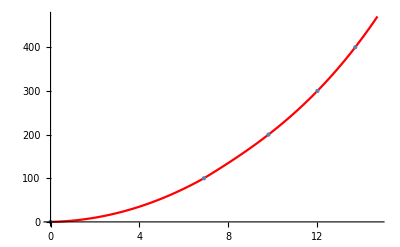

```mathematica
Show[Plot[distance[t],{t,0,timeBells[[5]]+1},PlotStyle->Red],ListPlot[ballBells,PlotStyle->PointSize[Large]]]
```

With the function interpolated is now easy to construct a map of distances values for different increasing values of time between the range of time data interpolated:

```mathematica
dt =Map[distance,{1,2,4}]
```

{2.33003,22.5906,113.002}

So it can be seen easily that when the time is doubled the space traveled is not doubled. The ratio between consecutive values can be obtained by this line of code:

```mathematica
Table[dt[[i]]/dt[[1]],{i,1,Length[dt]}]
```

{1.,9.69539,48.4981}

On the other side it can be also see that for equal intervals of time the distances are not increasing equally:

```mathematica
dt =Map[distance,{1,2,3,4,5,6,7}]
```

{2.33003,22.5906,59.4519,113.002,178.836,254.664,352.244}

```mathematica
increasing = dt - Map[distance,{1,1,2,3,4,5,6}]
```

{0.,20.2606,36.8613,53.5502,65.8338,75.8279,97.5799}

We can try to find a simple analytical expression of the interpolated function using the command InterpolatingPolynomial[ ] to the points ballBells:

```mathematica
InterpolatingPolynomial[ballBells,t]
```

400+(-7.4+t) (54.0541+(7.70507+(0.0436669+0.294764 (-5.3+t)) (-3.8+t)) t)

```mathematica
space[t_]=Expand[%]
```

0.-45.666 t+33.0019 t^2-4.81994 t^3+0.294764 t^4

That is approximately space[ t ] and now we check the result of that function in a the known values of time:

```mathematica
Map[space,timeBells]
```

{0.,100.,200.,300.,400.}

And finally we can start to make interesting questions with our students about physical hypothesis, approximations and argumentation:

.- What does the mathematical expression space[t] really means?
.- How should we interpret the cubic and quartic terms? and the first order term in t?
.- What happens if we interpolate the experimental points only to first order? And second order? For example:

```mathematica
distance = Interpolation[ballBells,, InterpolationOrder->2]
```

InterpolatingFunction[{{0., 7.4}}, <>][Null]

.- Which is now the best fitting interpolating function for our list of experimental points?
.- What happens if the slope of the plane is changed? and if the planet is changed?
.- Can we deduce the value of the gravity of the planet listening the sounds of the bells? How could we do that?
.- What piece of code would we need for this goal?
.- What if we construct physically a real inclined plane with bells and we register the sound of the bells?
.- How can we analyze with code the results of the real experiment?